```mathematica
Trail=Import["/Users/glassman/Downloads/Map.xlsx"];
```

```mathematica
DataSetTrail={};
```

```mathematica
For[n=1,n≤19336/2,n++,
DataSetTrail=Append[DataSetTrail,Trail[[1]][[2n]]];
];
DataSetTrail
```

{{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},{-79.5151,36.1008,0</gx:coord},«9651»,{-122.197,37.4097,0</gx:coord},{-122.166,37.3918,0</gx:coord},{-122.151,37.409,21</gx:coord},{-122.158,37.3964,0</gx:coord},{-122.155,37.4065,0</gx:coord},{-122.167,37.3983,0</gx:coord},{-122.167,37.3983,0</gx:coord},{-122.167,37.3983,0</gx:coord}}

```mathematica
PlotFromTrail={};
```

```mathematica
For[x=1,x<Length[DataSetTrail],x++,
PlotFromTrail = Append[PlotFromTrail,{ DataSetTrail[[x]][[1]],DataSetTrail[[x]][[2]]}]
];
```

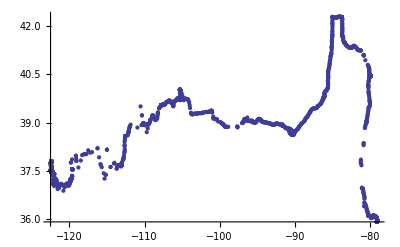

```mathematica
ListPlot[PlotFromTrail]
```